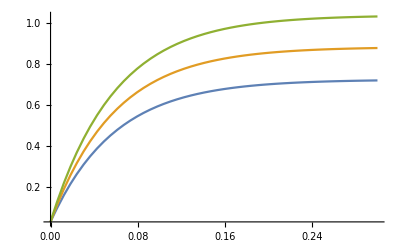

```mathematica
f[S_,Bn_]=1.10(1-Exp[-0.025Bn])(1 - Exp[-17S])+0.03;
Plot[{f[S,40],f[S,60],f[S,100]},{S,0.0,0.3},PlotRange->All]
```

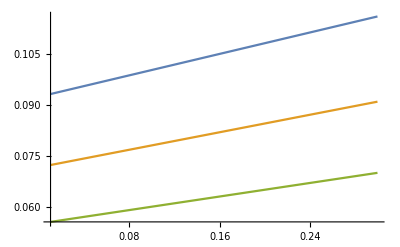

```mathematica
g[S_,Bn_]=2.5/Bn+0.03+0.5 S/(√Bn);
Plot[{g[S,40],g[S,60],g[S,100]},{S,0.01,0.3},PlotRange->All]
```

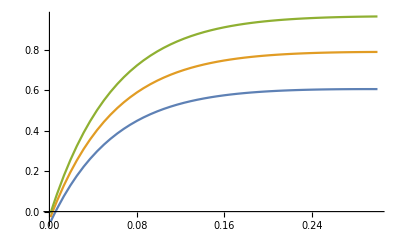

```mathematica
h[S_,Bn_]=f[S,Bn]-g[S,Bn];
Plot[{h[S,40],h[S,60],h[S,100]},{S,0.001,0.3},PlotRange->All]
```